```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Input

```mathematica
dataT1 = {99.999,82.705,73.282,62.195,51.109,52.772,48.891,50.0}/100;
dataTime =  {0,100, 200, 300, 400, 500, 600, 700};
lifetimedata = Transpose[{dataTime, dataT1}]
lifetimedataplot= Table[{lifetimedata⟦i⟧, ErrorBar[Sqrt[(Abs[lifetimedata⟦i⟧⟦2⟧  (1 - lifetimedata⟦i⟧⟦2⟧)])/200]]}, {i, 1, Length[lifetimedata]}];
```

{{0,0.99999},{100,0.82705},{200,0.73282},{300,0.62195},{400,0.51109},{500,0.52772},{600,0.48891},{700,0.5}}

```mathematica
Mean[{99.254,94.776,97.015,97.015}]
```

97.015

## Fit

```mathematica
decayfunc[tvar_, Γ_, A_] :=2/3 Exp[-tvar/Γ] + 1/3 ;
decayfunc[tvar_, Γ_, A_] :=1/2 Exp[-tvar/Γ] + 1/2 ;
decayfit = NonlinearModelFit[lifetimedata,decayfunc[tvar, Γ, A],{{Γ,10}, {A, -0.2}},tvar]
```

FittedModel[1/2+ⅇ^(-0.00493573 tvar)/2]

| Estimate | Standard Error | t-Statistic | P-Value
Γ | 202.604 | 20.9762 | 9.65878 | 0.0000705757
A | -0.2 | 0. | -∞ | 0.

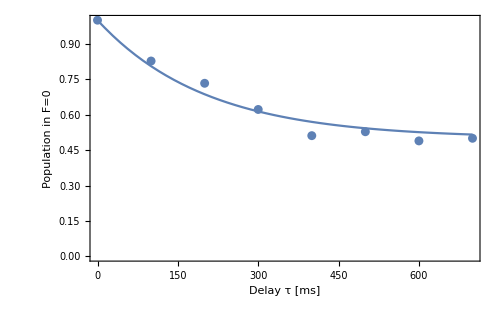

```mathematica
decayfit["ParameterTable"]
Show[ListPlot[lifetimedata],
Plot[decayfit["BestFit"]/.tvar-> t, {t, 0,Max[dataTime]}],
PlotRange-> {{0, Max[dataTime]},{0,1}},
Frame-> True, ImageSize-> 500, AxesOrigin-> False,FrameLabel->{{"Population in F=0",Null},{"Delay τ [ms]",Null}}, FrameStyle-> {Black, Bold}, LabelStyle-> {15}]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {Γ, 1.8372982906880355*^15, 6.441533603828744*^29, 2.8522684250160166*^-15, 1}}
```

| Estimate | Standard Error | t-Statistic | P-Value
Γ | 1.8373×10^15 | 6.44153×10^29 | 2.85227×10^-15 | 1